# Lecture 7 - Electric Field

"One must be alert for every opportunity to bring the students into the world where an electric field is not a symbol merely, but something that crackles." - Edward Purcell

### A Puzzle...

Four charges, q, −q, q, and −q, are located at equally spaced intervals on the x-axis. Their x values are −3a, −a, a, and 3a, respectively. Does there exist a point on the y-axis for which the force on a charge Q would be zero? If so, find the y value.
(Hint: Think back to last lecture, where we could easily determine whether there was such a point by a continuity argument. No equations necessary!)

Solution
We know that E_y=0 by symmetry, so we only need to worry about E_x.

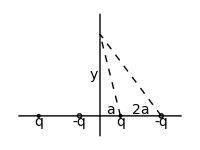

```mathematica
s=0.1;pt={0,4};ft=14;
centerPlot@Graphics[{Disk[{-3,0},s],Disk[{1,0},s],Circle[{-1,0},s],Circle[{3,0},s],Line[{{{-4,0},{4,0}},{{0,-1},{0,5}}}],Dashed,Line[{{{1,0},pt},{{3,0},pt}}],Text[Style["a",ft],{0.5,0.3}],Text[Style["2a",ft],{2,0.3}],Text[Style["y",ft],{-0.3,pt[[2]]/2}],Text[Style["q",ft],{-3,-0.3}],Text[Style["-q",ft],{-1,-0.3}],Text[Style["q",ft],{1,-0.3}],Text[Style["-q",ft],{3,-0.3}]},ImageSize->200]
```

We want the leftward contribution from the two middle charges to cancel the rightward contribution from the two outer charges. Thus

(2k q Q)/(a^2+y^2)a/((a^2+y^2)^(1/2))=(2k q Q)/((3a)^2+y^2)(3a)/(((3a)^2+y^2)^(1/2))

where the second factor on each side comes from taking the x-component. Simplifying yields

1/((a^2+y^2)^(3/2))=3/((9 a^2+y^2)^(3/2))

9 a^2+y^2=3^(2/3)(a^2+y^2)

y^2=a^2(3^(2/3)-9)/(1-3^(2/3))

y=a ((3^(2/3)-9)/(1-3^(2/3)))^(1/2)≈2.53a

In hindsight, we know that there must exist a point on the y-axis with F_x=0 by a continuity argument. For small y, the electric force points leftward, because the two middle charges dominate. But for large y, the electric force points rightward, because the two outer charges dominate. (This is true because for large y, the distances to the four charges are all essentially the same, but the slope of the lines to the outer charges is smaller than the slope of the lines to the middle charges (it is 1/3 as large). So the x-component of the force due to the outer charges is 3 times as large, all other things being equal.) Therefore, by continuity, there must exist a point on the y-axis where F_x equals zero. □

### Theory

#### Electric Field

Suppose you have a charge distribution. You can probe the effects of this charge distribution by placing a charge q at a point (x,y,z) and measuring the force F⃗ on that charge. The electric field at the point (x,y,z) is defined as (F⃗)/q. You can simply think of the electric field as a matter of convenience - with it we no longer need to explicitly state that we are considering a charge q. If we had instead used a charge 2q, the force on that charge would have doubled, but the electric field stays the same.

Formally, given point charges q_1,q_2... q_N, the electric field at a point (x,y,z) equals

E⃗[x,y,z]≡∑_(j=1)^N (k q_j)/r_j^2(r̂)_j

where (r⃗)_j is the vector from the j^th charge to the point (x,y,z). Therefore, the force on a charge q placed at (x,y,z) would be F⃗=q E⃗.

For a continuous 3D charge distribution ρ (pronounced "rho"),

E⃗[x,y,z]≡∫(k ρ[x',y',z']ⅆx'ⅆy'ⅆz')/r^2 r̂

where r⃗ is the vector from point (x',y',z') to the point (x,y,z). ρ[x',y',z'] denotes the charge within the infinitesimal volume element at (x',y',z'). Note that this integral only needs to be carried out over the volume of all charged objects. However, we could also carry it out over all of space, since ρ=0 in all other regions of space.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

We will typically write the above result for the electric field as

E⃗=∫(k ⅆq)/r^2 r̂

where ⅆq is the charge from the infinitesimal volume element that we use to break up the charge density. For 1D charge densities λ (pronounced “lambda”) such as an infinite line of charge, we insert ⅆq=λⅆs into Equation (TextNumbered) where ⅆs integrates along the line. When we deal with 2D charge density σ (pronounced “sigma”) such as a plane of charge or a spherical shell of charge, we insert ⅆq=σⅆa within Equation (TextNumbered) where ⅆa integrates along the surface. For 3D volume charge densities, ⅆq=ρⅆv. In summary,

E⃗=Piecewise[{{∑_j (k q_j)/r_j^2(r̂)_j, point charges}, {∫(k λⅆs)/r^2 r̂, 1,D charge distribution}, {∫(k σⅆa)/r^2 r̂, 2,D charge distribution}, {∫(k ρⅆv)/r^2 r̂, 3,D charge distribution}}]

#### A Note about Coordinate Systems

Equation (TextNumbered) uses Cartesian coordinates, which is a specific coordinate system. I will introduce most formulas in this class using Cartesian coordinates, but you can always transform these into coordinate-free results as follows. First, write the Cartesian coordinate volume element as ⅆv=ⅆx'ⅆy'ⅆz' and denote the location of your point of interest by r⃗=⟨x,y,z⟩ and the location of the infinitesimal volume element as r⃗'=⟨x',y',z'⟩.

Note that in the denominator of Equation (TextNumbered), r^2 (which is no longer valid notation since we have now defined a new vector r⃗) represents the quantity (x-x')^2+(y-y')^2+(z-z')^2=(|r⃗-r⃗'|)^2. Similarly, we need to translate the r̂ in Equation (TextNumbered) into our new notation as (r⃗-r⃗')/(|r⃗-r⃗'|).

Using all of these new definitions, Equation (TextNumbered) can be rewritten in the coordinate-free form as

E⃗[r⃗]≡∫(k ρ[r⃗']ⅆv)/(|r⃗-r⃗'|)^2(r⃗-r⃗')/(|r⃗-r⃗'|)

From here, we are free to use whatever coordinate system we want. The shape of the charge distribution will typically dictate which coordinate system is easiest to use. As a reminder, the volume elements at a point (x,y,z) in Cartesian, spherical, and cylindrical coordinates are

ⅆv={ⅆxⅆyⅆz | Cartesian
r^2 Sin[θ]ⅆrⅆθⅆϕ | spherical
ρ ⅆρ ⅆθ ⅆz | cylindrical

#### Advanced Sections: Charge Density of a Point Charge

We intuitively know what we mean when say a point charge q: we are referring to a finite charge which resides in a single, infinitesimal point in space. But the precise mathematical details of a point charge are subtle.

One excellent way to think of a point charge q is to consider a solid sphere of radius R with charge density ρ=Q/(4/3 π R^3) centered at the origin, by which we mean

ρ=Piecewise[{{Q/(4/3 π R^3), r<R}, {0, r>R}}]

A point charge is simply the limit when the radius shrinks to zero, R→0. But note that the charge density behaves very strangely in this limit; namely it equals to 0 at all points in space except r=0, at which point ρ→∞. But ρ becomes infinitely large in a very special way, since integrating ρ across the entire volume does not yield ∞ but rather yields the finite charge q. So in the limit R→0, the integral

∫_-ϵ^ϵ ∫_-ϵ^ϵ ∫_-ϵ^ϵ ρ[x,y,z]ⅆxⅆyⅆz=q

regardless of how small ϵ is! In case you are not amazed by this result, note that for any standard function (like ρ=x^2 or ρ=E^(x y z) or any other non-infinite function you can think of), this integral would go to zero for sufficiently small ϵ. Formally, we call the charge density ρ for a point charge a delta function,

ρ[x,y,z]=q δ[x]δ[y]δ[z]

where each of the three delta functions δ[x], δ[y], and δ[z] obeys

δ[x]=Piecewise[{{0, x≠0}, {∞, x=0}}]

but in a very special manner so that for any function f[x],

∫_x_1^x_2 f[x]δ[x]ⅆx=f[0]

provided that x_1<0 and x_2>0 (otherwise, the integral yields 0 everywhere because of the delta function).

We usually sweep this complexity under the rug by simply writing out all of the major formulas in terms of both charge distributions and point charges. For example, the electric field is given by

E⃗[x,y,z]≡∫(k ρ[x',y',z']r̂ ⅆx'ⅆy'ⅆz')/r^2

for charge distributions and

E⃗[x,y,z]≡∑_(j=1)^N (k q_j(r̂)_(0,j))/(r_(0,j)^2)

for point charges. However, these delta functions will actually appear all the time in this class. Infinite sheets are delta functions in one direction (the infinitely thin direction). Line charges are delta functions in two directions (along the two perpendicular directions to the line’s axis). And point charges are delta functions in all three directions. We won’t have too much more to say about delta functions in this class (we will just automatically use the appropriate formula), but you will definitely see them again in future classes.

#### Some Basic Example

Let’s look at some simple examples to see how Equation (TextNumbered) can be used.

Example (Point charges)
A point charge q_1 resides at (x,0,0) while another point charge q_2 resides at (0,y,0). What is the electric field at the origin?

Solution
We handle the charges one at a time. The charge q_1 exerts an electric field (E⃗)_q_1=(k q_1)/x^2(-x̂) at the origin, while the charge q_2 exerts a field (E⃗)_q_2=(k q_2)/y^2(-ŷ). The net electric field at the origin equals the sum of these two contributions,

E⃗=-(k q_1)/x^2 x̂-(k q_2)/y^2 ŷ

Since the two charges and the origin all lie in the x-y plane, there is no z-component for the electric field at the origin. □

Example (1D charge distribution)
A line with non-uniform charge density λ[z] lies between z∈[0,L] on the z-axis. What is the electric field at the origin? What is the integral for the case when the charge density λ[z]=λ is constant?

Solution
Break the line of charge into small chunks between z and z+ⅆz. The distance between each chunk and the origin is z, and the direction from the chunk to the origin is -ẑ. Thus, the electric field at the origin will be given by

E⃗=∫_0^L (k λ[z]ⅆz)/z^2(-ẑ)=-k ẑ∫_0^L (λ[z]ⅆz)/z^2

Note that we can pull out the constants (k and ẑ) from the integral, but we cannot carry out the integral unless we are given the explicit charge distribution. In the special case where λ[z]=λ is constant, the integral becomes

E⃗=-k ẑ∫_0^L λⅆz/z^2=-k λ ẑ∫_0^L ⅆz/z^2

which diverges. This is because the charge at z=0 exerts an infinitely large electric field at the origin. □

```mathematica
Integrate[-(k λ)/z^2,{z,0,L}]
```

Example (2D charge distribution)
A square with non-uniform charge density σ[x,y] lies within x∈[0,L] and y∈[0,L]. What is the electric field at the origin? What is the integral for the case when the charge density σ[x,y]=σ is constant?

Solution
As above, we break the line of charge into small chunks chunks. More precisely, at each point (x,y) we will consider the infinitesimal area of the square bounded by (x,y), (x+ⅆx,y), (x,y+ⅆy), and (x+ⅆx,y+ⅆy).

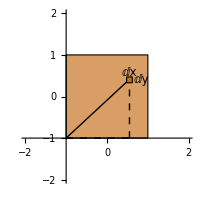

```mathematica
ft=12;a=0.07;b=0.07;
centerPlot@Show[Plot[0,{x,-2,2},PlotStyle->None,PlotRange->{{-2,2},{-2,2}},AspectRatio->1,AxesStyle->FontSize->0.01,AxesOrigin->{-1,-1},ImageSize->200],Graphics[{EdgeForm[Black],FaceForm[Lighter@color3],Rectangle[{-1,-1},{1,1}],Line[{{-1,-1},0.88{0.55,0.4}}],{FaceForm[color3],Rectangle[{0.55,0.4}-{a,b},{0.55,0.4}+{a,b}]},Dashed,Line[{{{-1,-1},{0.55,-1}},{{0.55,-1},{0.55,0.8*0.4}}}],Text[Style["ⅆx",ft],{0.55,0.58}],Text[Style["ⅆy",ft],{0.85,0.4}]}]]
```

The charge on this small patch is given by σ[x,y]ⅆxⅆy, and the distance between this patch and the origin is (x^2+y^2)^(1/2). Finally, the (normalized) direction from the infinitesimal area element to the origin is given by -(x x̂+y ŷ)/((x^2+y^2)^(1/2)). Thus, the electric field at the origin will be given by

E⃗=∫_0^L ∫_0^L (k σ[x,y]ⅆxⅆy)/(x^2+y^2)(-(x x̂+y ŷ)/((x^2+y^2)^(1/2)))

In the case where the charge distribution σ[x,y]=σ is uniform, the integral again diverges, as is demonstrated by the Mathematica code below,

```mathematica
Integrate[(k σ)/(x^2+y^2){-x,-y}/((x^2+y^2)^(1/2)),{x,0,L},{y,0,L}]
```

Example (3D charge distribution)
A cube with a non-uniform charge density ρ[x,y,z] lies within x∈[0,L], y∈[0,L], and z∈[0,L]. What is the electric field at the origin? What is the integral for the case when the charge density ρ[x,y,z]=ρ is constant?

```mathematica
centerPlot@DynamicModule[{ds=0.25,k=0.1,pts},
pts=Flatten[Table[{x,y,z},{z,0,1-ds,ds},{y,0,1-ds,ds},{x,0,1-ds,ds}],2];
Manipulate[
With[{x=pts[[index,1]],y=pts[[index,2]],z=pts[[index,3]]},
pt={x+ds/2,y+ds/2,z+ds/2};
r=Norm@pt;
Graphics3D[{{Opacity[0.2],Cuboid[{0,0,0},{1,1,1}]},Cuboid[{x,y,z},{x,y,z}+ds{1,1,1}],{Dashed,Line[{pt,{0,0,0}}]},{Thick,Darker@Blue,Arrow[{{0,0,0},-Min[k/r^2,0.9]Normalize@pt}],Text[Style["ⅆE⃗",18,FontFamily->"Times"],-1/2 Min[k/r^2,0.9]Normalize@pt+0.08{-1,1,1}]}},Boxed->False,PlotRange->{{-0.5,1.1},{-0.5,1.1},{-0.5,1.1}},PlotLabel->Style["Electric Field at the Corner of a Cube",14,FontFamily->"Times"],ViewAngle->0.389,ViewCenter->{{0.5,0.5,0.5},{0.515,0.485}},ViewPoint->{1.344,-2.616,1.674},ViewVertical->{0.053,-0.102,0.993}]
]
,{{index,1,"Integrate"},1,Length@pts,1}]
]
```

Solution
As above, we break the line of charge into small chunks at the point (x,y,z), with each chunk having width ⅆx, length ⅆy, and height ⅆz. The charge in each chunk is given by ρ[x,y,z]ⅆxⅆyⅆz and the distance between this chunk and the origin is (x^2+y^2+z^2)^(1/2). The (normalized) direction from the infinitesimal volume element to the origin is given by -(x x̂+y ŷ+z ẑ)/((x^2+y^2+z^2)^(1/2)). Thus, the electric field at the origin will be given by

E⃗=∫_0^L ∫_0^L ∫_0^L (k ρ[x,y,z]ⅆxⅆyⅆz)/(x^2+y^2+z^2)(-(x x̂+y ŷ+z ẑ)/((x^2+y^2+z^2)^(1/2)))

In the case where the charge distribution ρ[x,y]=ρ is uniform, we can compute the integral using Mathematica,

```mathematica
N@Integrate[(k ρ)/(x^2+y^2+z^2){-x,-y,-z}/((x^2+y^2+z^2)^(1/2)),{x,0,L},{y,0,L},{z,0,L},Assumptions->0<L]
```

{-0.969388 k L ρ,-0.969388 k L ρ,-0.969388 k L ρ}

A remarkable thing happens - the integral is finite! You may wonder how in the world this could happen, since the infinitesimal volume element at (x,y,z)=(0,0,0) is infinitely close to the origin and hence should exert an infinite electric field. To understand this result, consider an infinitesimal volume element at a point r⃗=⟨x,y,z⟩, and now imagine reeling this point into the origin so that the volume element is brought to α r⃗ where α starts at 1 and then goes to 0. The magnitude of the electric field contribution from this infinitesimal chunk (ignoring the direction for the moment) will be

ⅆE=(k ρⅆv)/(α^2 r^2)

So the denominator does indeed go to zero, but it is overpowered by the numerator, which represents an even smaller number since ⅆv=ⅆxⅆyⅆz can be effectively thought of as three infinitely small quantities, whereas the denominator only has two infinitely small quantities (from the α^2). Therefore, when we integrate over this single singular point in 3D we will still get a finite value. In contrast, in 1D the integral must blow up (because the numerator will only be λ ⅆz which has one infinitely small quantity) and in 2D both the numerator (σ ⅆxⅆy) and the denominator have two infinitely small quantities (such cases are effectively ∞^2/∞^2, which could result in any value and in this case happens to still diverge).

If you are not completely satisfied with the above argument, consider the integral of the function 1/r^2 in N-dimensions, where the integral is done over the N-dimensional ball of radius R. The Mathematica code below demonstrates that this integral also diverges for 1D and 2D, but not for 3D.

```mathematica
(* 1D *)
Integrate[1/z^2,{z,-R,R}]
(* 2D *)
Integrate[1/r^2 r,{r,0,R},{θ,0,2π}]
(* 3D *)
Integrate[1/r^2 r^2 Sin[θ],{r,0,R},{θ,0,π},{ϕ,0,2π}]
```

### Visualizing the Electric Field

The visualization below shows the electric field from several point charges (direction given by the arrows and the magnitude given by how light the arrows are). You can add or remove point charges using the "More +/-" and "Less +/-" buttons.

```mathematica
arrowSize=5;
labels={"    Electric Field    ","     More +     ","     More -     ","Electric Potential","     Less +     ","     Less -     "};
{numPos,numNeg}={1,0};
centerPlot@Manipulate[
If[MemberQ[opts,labels[[2]]],numPos++;opts=DeleteCases[opts,labels[[2]]]];
If[MemberQ[opts,labels[[3]]],numNeg++;opts=DeleteCases[opts,labels[[3]]]];
If[MemberQ[opts2,labels[[5]]],numPos--;opts2=DeleteCases[opts2,labels[[5]]]];
If[MemberQ[opts2,labels[[6]]],numNeg--;opts2=DeleteCases[opts2,labels[[6]]]];
positive={p1,p3,p5,p7}[[;;numPos]];
negative={p2,p4,p6,p8}[[;;numNeg]];
arrow=Table[{GrayLevel[Clip[Norm[Total[({x,y}-#)/Norm[{x,y}-#]^3&/@positive]-Total[({x,y}-#)/Norm[{x,y}-#]^3&/@negative]]^(1/3),{0,0.004^(1/3)}]/0.004^(1/3)],Arrow[{{x,y}-0.6arrowSize(Normalize[Total[({x,y}-#)/Norm[{x,y}-#]^3&/@positive]-Total[({x,y}-#)/Norm[{x,y}-#]^3&/@negative]]),{x,y}+2.2arrowSize(Normalize[Total[({x,y}-#)/Norm[{x,y}-#]^3&/@positive]-Total[({x,y}-#)/Norm[{x,y}-#]^3&/@negative]])}]},{x,-90,90,22},{y,-90,90,22}];
arrowPoints=Flatten[Table[{x,y},{x,-90,90,22},{y,-90,90,22}],1];
Show[Graphics[{{Black,Rectangle[{-100,-100},{100,100}]}},PlotRange->100,ImageSize->{400,400}],If[MemberQ[opts2,labels[[4]]],ContourPlot[Total[1/Norm[{x,y}-#]&/@positive]-Total[1/Norm[{x,y}-#]&/@negative],{x,-100,100},{y,-100,100},Contours->20,ClippingStyle->Automatic,ColorFunction -> (Blend[{Darker@Blue,Black,Darker@Red},#]&),Frame->False,ImageSize->{400,400}],Sequence@@{}],If[MemberQ[opts,labels[[1]]],Graphics[{{Thickness[0.013],Arrowheads[{0.01,0.045}],arrow,{Black,PointSize[0.002],Point[arrowPoints]}}},PlotRange->100,ImageSize->{400,400}],Sequence@@{}],Graphics[{{Lighter@Red,PointSize[0.04],Point[#],White,Text[Style["+",20,Bold],#+{0.3,0.5}]}&/@positive,{Lighter@Blue,PointSize[0.04],Point[#],White,Text[Style["-",20,Bold],#+{0.3,0.5}]}&/@negative}]],
{{opts,{labels[[1]]},"     "},labels[[1;;3]],ControlType->TogglerBar,Appearance->"Row"},{{opts2,{},"     "},labels[[4;;6]],ControlType->TogglerBar,Appearance->"Row"},
{{p1,{0,0}},Locator,Appearance->None},{{p2,RandomReal[{-50,50},2]},Locator,Appearance->None},
{{p3,RandomReal[{-50,50},2]},Locator,Appearance->None},{{p4,RandomReal[{-50,50},2]},Locator,Appearance->None},
{{p5,RandomReal[{-50,50},2]},Locator,Appearance->None},{{p6,RandomReal[{-50,50},2]},Locator,Appearance->None},
{{p7,RandomReal[{-50,50},2]},Locator,Appearance->None},{{p8,RandomReal[{-50,50},2]},Locator,Appearance->None},Paneled->False]
```

We will learn about the electric potential in a few classes. For now, consider the following questions:

If we stick one positive charge in one corner and a negative charge in the opposite corner, in which direction will the arrows point along the diagonal, and where will the magnitude of the electric field be largest (i.e. where will the arrows be brightest)?

How can you make all of the arrows on the middle horizontal line (y=0) point directly upwards?

If we put one positive and one negative charge right on top of one another, what will happen?

With two positive and two negative charges, how can you make the arrow in the center become dark (i.e. have zero electric field) while still keeping all of the other arrows on the screen bright?

Here are the answers to these questions:
(1) Along the diagonal connecting the two point charges, the electric field points from the plus charge and towards the minus charge. The magnitude of the electric field from a point charge goes as 1/r^2, so the arrows will be brightest near the two point charges at the two corners.
(2) If you put the minus charge at any point (x,y) and the plus charge at the point (x,-y), then all of the arrows on the line y=0 will have to point upwards. Let’s assume the point charges have charge +q and -q, and let us consider the electric field of a point at (X,0). The electric field from the minus charge will be (k q ⟨x-X,y⟩)/(((x-X)^2+y^2)^(3/2)) and the electric field from the plus charge will be (k q ⟨-(x-X),y⟩)/(((x-X)^2+y^2)^(3/2)), so the x-components of these two contributions will vanish.
(3) The two charges will exactly cancel out (by the principle of superposition, they must be identical to a single particle with charge q+(-q)=0), and hence all of the arrows will become completely dark.
(4) You can build a square around the center arrow, with charges of the same on opposite diagonals. The two plus charges will cancel each other out, and so will the two negative charges, but only for the center arrow. More generally, any distribution where the two positive charges are at (x,y) and (-x,-y) while the two negative charges are at (X,Y) and (-X,-Y) will make the center arrow dark.

### Problems

#### Extra Problem: Concurrent Field Lines

Example
A semicircular wire with radius R has uniform charge density −λ. Show that at all points along the “axis” of the semicircle (the line through the center, perpendicular to the plane of the semicircle, as shown in the following figure), the vectors of the electric field all point toward a common point in the plane of the semicircle. Where is this point?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
Assume that the "axis" of the semicircle lies along the y-axis. By symmetry, the x-component of the electric field equals zero. We will consider the electric field at the point (0,0,z).

If we parameterize the semicircle by an angle θ going from 0 to π, then the bit of charge λ R ⅆθ will create an electric field with magnitude (k (λ Rⅆθ))/(R^2+z^2) at the point (0,0,z). What is the component of this electric field in the y-direction and z-direction? Since the charge lies at (R Cos[θ],R Sin[θ],0), the vector from the point (0,0,z) to this charge (points in the same direction as the electric field contribution from this charge) equals ⟨R Cos[θ],R Sin[θ],-z⟩. So the component in the y-direction and z-direction equals the magnitude of the electric field multiplied by (R Sin[θ])/(√(R^2+z^2)) and -z/(√(R^2+z^2)), respectively. Therefore, the electric field in the y-direction and z-direction equals

E_y=∫_0^π (k (λ Rⅆθ))/(R^2+z^2)(R Sin[θ])/((R^2+z^2)^(1/2))=(2k R^2 λ)/((R^2+z^2)^(3/2))

E_z=∫_0^π (k (λ Rⅆθ))/(R^2+z^2)-z/((R^2+z^2)^(1/2))=-(k π R z λ)/((R^2+z^2)^(3/2))

(You should also setup and carry out the integration for E_x and prove that it is zero algebraically, even though we know that it must be so geometrically.)

Therefore, the electric field line passes through the point (0,0,z) with E_z/E_y=-z/((2 R)/π). When this line moves down along the z-axis by z it moves up along the y-axis by (2R)/π, so that all of the lines merge at the point (0,(2R)/π,0). Note that this point is independent of z, as desired.

This point also happens to be the "center of charge" of the semi-circle, or equivalently, the center of mass of a semicircle with a uniform mass density (which by symmetry lies on the y-axis at the point y_cm=(∫y ⅆm)/(∫ⅆm)=(∫_0^π (R Sin[θ])(λ R ⅆθ))/(∫_0^π λ R ⅆθ)=(2 R^2 λ)/(π R λ)=(2R)/π). This result is consistent with the following intuitive fact (which you can easily prove for yourself): far away from a distribution of charges, the electric field points approximately towards the center of the charge of the distribution. For nearby points, it generally doesn’t, although it happens to (exactly) point in that direction for points on the axis of the present setup. □

#### Advanced Section: Qualitative Field from a Hemisphere

In the example "Field from a Semicircle" above, we found the electric field at the center of a semicircle of radius R with charge Q distributed uniformly across it, which has magnitude E_semicircle=(2k Q)/(π R^2).

Now consider the corresponding problem for a hemisphere: compute the electric field at the center of a hemisphere of radius R with charge Q distributed uniformly across it. Call the answer E_hemisphere.

Is E_hemisphere less than, equal to, or greater than E_semicircle?
(Hint: Build up the hemisphere by gluing together a bunch of semicircles and compare the charge distribution of what you just built.)

```mathematica
centerPlot@Manipulate[
inc=spacing;inc2=π/40.;
pts=N@Flatten[Table[{Cos[θ],0,Sin[θ]}.RotationMatrix[θrot,{0,0,1}]+(* A little jitter so that the points at (0,0,1) will not be perfectly overlapping and hence will be visibly less opaque *)RandomReal[10^-3,3],{θ,0,π,inc2},{θrot,0,θrotMax,inc}],1];
plots=Table[{Cos[θ],0,Sin[θ]}.RotationMatrix[θrot,{0,0,1}],{θrot,0,θrotMax,inc}];
Show[If[showCharges,Graphics3D[{Opacity[0.63*spacing],Red,Ball[#,0.04]&/@pts},PlotRange->1.05{{-1,1},{-1,1},{-0.1,1}}],ParametricPlot3D[plots,{θ,0,π},PlotRange->1.05{{-1,1},{-1,1},{-0.1,1}},Axes->False]],Graphics3D[{PointSize[0.02],Point[{0,0,0.01}]}],ViewPoint->{1.2284458642133287,-2.728726942004659,1.5795474145067858}]
,{{θrotMax,0,"# of semicircles"},0,π-0.01},{{spacing,π/10.,"closeness"},π/10.,π/40.},{{showCharges,False,"show charges"},{False,True}}]
```

Solution
How can we relate a hemisphere with a semicircle? We could imagine gluing together N semicircles at their apex, slightly rotated from each other, with each semicircle carrying a charge Q/N. In the limit as N→∞, this shape would certainly be a hemisphere, and the resulting force on charge q would still be N(2k q Q/N)/(π R^2)=F_semicircle. But how does this charge distribution compare to a hemisphere with uniform charge distribution?

Clearly the hemisphere that we constructed out of semicircles would have a lot of charge concentrated at its apex. Said another way, the semicircle’s charge is generally higher up than the hemisphere’s. Therefore, we must have F_semicircle>F_hemisphere because the charge at the top contributes significantly more to the total force than the charge near the base (where only the vertical component contributes to the overall force).

In today’s lecture, we will calculate the force in the example "Field from a Hemisphere" and find it to be F_hemisphere=(k q Q)/(2 R^2) (although we will actually calculate the electric field) which is indeed smaller than F_semicircle by a factor of π/4. □

#### Quantitative Field from a Hemisphere

Example
1. What is the electric field at the center of a hollow hemispherical shell with radius R and uniform surface charge density σ?
2. Use this result to compute the electric field at the center of a solid hemisphere with radius R and uniform volume charge density ρ.

```mathematica
arc[r_,θ_,{ϕ1_, ϕ2_}]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{ϕ,ϕ1,ϕ2,(ϕ2-ϕ1)/Round[((ϕ2-ϕ1)/(2π))180.]}]]
arc[r_,{θ1_,θ2_},ϕ_]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
PolarToCartesian[{r_,θ_,ϕ_}]:=
r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]}
sphericalGraphic = With[{hemisphere = First[ParametricPlot3D[
{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{ϕ,0,π/2},{θ,0,2π},Boxed->False,Mesh->None,Axes->None]],
al=1.2,
tl=1.3
},
Graphics3D[{
Arrowheads[Small],
Arrow[al{{{-1,0,0},{1,0,0}},{{0,-1,0},{0,1,0}},{{0,0,-.1/1.1},{0,0,1}}}],
Text["x",tl{1,0,0}],
Text["y",tl{0,1,0}],
Text["z",tl{0,0,1}],
With[{ϕ=45°,θ=45°,ar=.25,tr=.35},
{
{Arrow[{{0,0,0},PolarToCartesian[{1,θ,θ}]}]},
arc[1,ϕ,{0,θ}],
arc[Sin[θ],{0,ϕ},π/2],
Line[{{0,0,0},PolarToCartesian[{Sin[θ],ϕ,π/2}],
PolarToCartesian[{1,ϕ,θ}]}],
arc[ar,{0,ϕ},π/2],
arc[ar,ϕ,{0,θ}],
Text["ϕ",PolarToCartesian[{tr,ϕ/2,π/2}],{-1,1}],
Text["θ",PolarToCartesian[{tr,θ,θ/2}],{0,-1}]
}],
{Opacity[.5],hemisphere}
},Boxed->False,ViewAngle->0.23834282811973823,ViewCenter->{{0.5,0.5,0.5},{0.5232207158863535,0.648727549337275}},ViewPoint->{2.72,-0.92,1.78},ViewVertical->{0.07,-0.037,1.83},ImageSize->200]
];
centerPlot@sphericalGraphic
```

-Graphics3D-

Solution
1. This is a straightforward exercise of your Calculus skills. Recall that the small patch of surface between angle θ and θ+ⅆθ, as well as between ϕ and ϕ+ⅆϕ has area R^2 Sin[θ]ⅆϕⅆθ.

Note that by the symmetry of the hemisphere around the z-axis, the electric field at the center must point along the z-axis (more precisely, along the -z-axis if σ>0). More specifically, the electric field from the small patch at (θ,ϕ) not pointing along the z-axis will be canceled by the small patch at (θ,ϕ+π). Thus, the electric field will point in the -ẑ direction, and its magnitude is given by

E⃗=∫_0^(π/2) ∫_0^(2π) (k (σ R^2 Sin[θ]ⅆϕⅆθ))/R^2 Cos[θ](-ẑ)

where the final Cos[θ] picks out the z-component of the electric field. Computing this integral,

E⃗=∫_0^(π/2) 2π k σ Sin[θ]Cos[θ]ⅆθ (-ẑ)
=π k σ (-ẑ)

If we now define the total charge Q on the spherical shell, then σ=Q/(2π R^2) and the electric field is given by

E⃗=-(k Q)/(2 R^2) ẑ

As discussed in the previous problem, this is indeed smaller than the electric field at the center of a semicircle with charge Q and radius R, which we found above equals E⃗=-(2k Q)/(π R^2)≈-0.637(k Q)/R^2.

2. We break up the solid hemisphere into hemispherical shells, each with thickness ⅆr. The charge on such a shell equals ρ 4π r^2 ⅆr while the charge on a hemispherical shell of radius r equals σ 4 π r^2. Setting these two equal, ρ 4π r^2 ⅆr=σ 4 π r^2, yields σ=ρ ⅆr.

The total electric field from all of the hemispherical shells is now straightforward to compute

E⃗=∫π k σ (-ẑ)
=∫_0^R π k ρ ⅆr (-ẑ)
=π k ρ R (-ẑ)

Of course, we could have also computed this by simply integrating over the entire volume of the hemispherical shell

E⃗=∫_0^R ∫_0^(π/2) ∫_0^(2π) (k (ρ r^2 Sin[θ]ⅆϕⅆθⅆr))/r^2 Cos[θ](-ẑ)

which would clearly result in the same result found above (since after canceling the r^2 from the numerator and denominator, this is the same integral we did in Part 1, and the final integral of ⅆr simply multiplies the result by R). □